## Solutions S_01and S_02

```mathematica
ClearAll["Global`*"]
```

```mathematica
bar[I0_,Ak_]:=I0*Ak;
(* The Intrinsic Spin terms *)
Subscript[P, 31][Spin_,j_,I0_,A1_,A3_]:=(2Spin-1)(bar[I0,A3]-bar[I0,A1])+2*j*bar[I0,A1];
Subscript[P, 21][Spin_,j_,I0_,A1_,A2_]:=(2Spin-1)(bar[I0,A2]-bar[I0,A1])+2*j*bar[I0,A1];
(* The Single-particle terms *)
Subscript[Q, 31][Spin_,j_,I0_,A1_,A3_]:=(2j-1)(bar[I0,A3]-bar[I0,A1])+2Spin*bar[I0,A1];
Subscript[Q, 21][Spin_,j_,I0_,A1_,A2_]:=(2j-1)(bar[I0,A2]-bar[I0,A1])+2Spin*bar[I0,A1];
(* The triaxial terms *)
Subscript[G, 1][j_,γ_]:=(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]);
Subscript[G, 2][j_,γ_]:=(2j-1)/(j(j+1))2 √3 Sin[γ*π/180];
```

### Define S_01 and S_02

```mathematica
Subscript[S, 01][I0_,Spin_,j_,γ_,A1_,A2_,A3_]:=(4*Spin*j*bar[I0,A3]^2-Subscript[P, 31][Spin,j,I0,A1,A3]*Subscript[Q, 31][Spin,j,I0,A1,A3])/(Subscript[P, 31][Spin,j,I0,A1,A3]*Subscript[G, 1][j,γ]);
Subscript[S, 02][I0_,Spin_,j_,γ_,A1_,A2_,A3_]:=(4*Spin*j*bar[I0,A2]^2-Subscript[P, 21][Spin,j,I0,A1,A3]*Subscript[Q, 21][Spin,j,I0,A1,A3])/(Subscript[P, 21][Spin,j,I0,A1,A3]*Subscript[G, 2][j,γ]);
```

### Numerical parameters

```mathematica
ak={0.01,0.3,0.9};
```

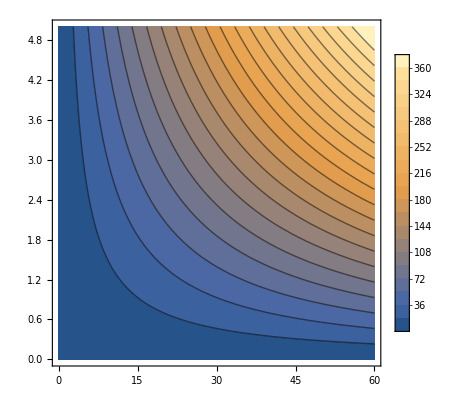

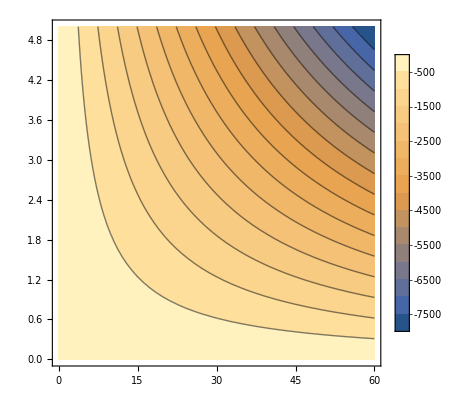

```mathematica
maxvalS01=Subscript[S, 01][60*5,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]];
maxvalS02=Subscript[S, 02][60*5,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]];
cpS01=ContourPlot[{(Subscript[S, 01][x*y,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]])},{x,0,60},{y,0,5},Contours->20,ContourStyle->Directive[Black],PlotLegends->Automatic];
cpS02=ContourPlot[{(Subscript[S, 02][x*y,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]])},{x,0,60},{y,0,5},Contours->15,ContourStyle->Directive[Black],PlotLegends->Automatic];
Show[cpS01]
Show[cpS02]
```

```mathematica
Subscript[F, 1][I0_,V_,Spin_,j_,γ_,A1_,A2_,A3_]:=Subscript[P, 31][Spin,j,I0,A1,A3]*Subscript[G, 1][j,γ]*(I0*V)+Subscript[P, 31][Spin,j,I0,A1,A3]*Subscript[Q, 31][Spin,j,I0,A1,A3]-4Spin*j*bar[I0,A3]^2;
Subscript[F, 2][I0_,V_,Spin_,j_,γ_,A1_,A2_,A3_]:=Subscript[P, 21][Spin,j,I0,A1,A2]*Subscript[G, 2][j,γ]*(I0*V)+Subscript[P, 21][Spin,j,I0,A1,A2]*Subscript[Q, 21][Spin,j,I0,A1,A2]-4Spin*j*bar[I0,A2]^2;
```

```mathematica
solutionF1=Values@Solve[Subscript[F, 1][I0,x,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]]==0,x][[1,1]];
solutionF2=Values@Solve[Subscript[F, 2][I0,x,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]]==0,x][[1,1]];
```

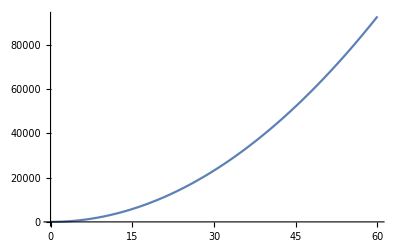

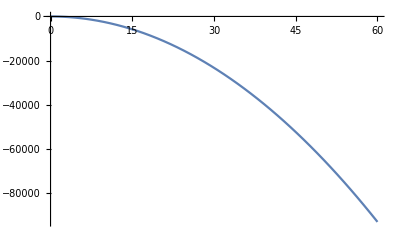

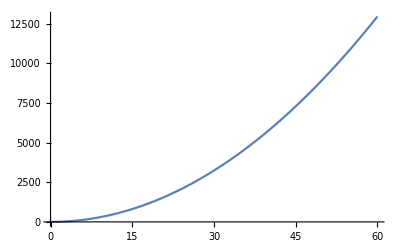

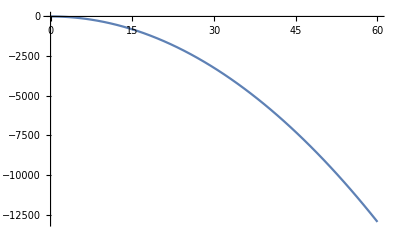

```mathematica
Plot[Subscript[F, 1][x,solutionF1+1,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]],{x,0,60}]
Plot[Subscript[F, 1][x,solutionF1-1,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]],{x,0,60}]
Plot[Subscript[F, 2][x,solutionF2+1,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]],{x,0,60}]
Plot[Subscript[F, 2][x,solutionF2-1,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]],{x,0,60}]
```

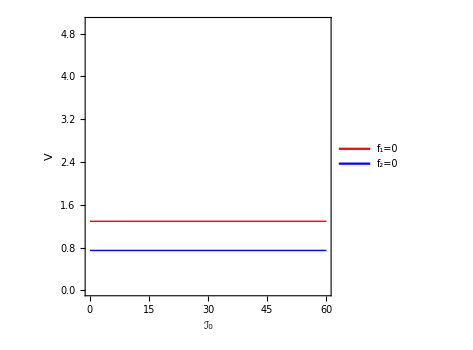

```mathematica
fig=Plot[{solutionF1,solutionF2},{x,0,60},PlotRange->{{0,60},{0,5}},Frame->True,Axes->False,AspectRatio->1,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},FrameLabel->{"ℐ_0","V"},ImageSize->350,PlotLegends->Placed[{"f_1=0","f_2=0"},{0.7,0.8}]];
Show[fig]
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/F_solutions.pdf",Show[fig]];
```